```mathematica
γ=0.5772156649;
EA[x_]:=Log[x]+γ;
```

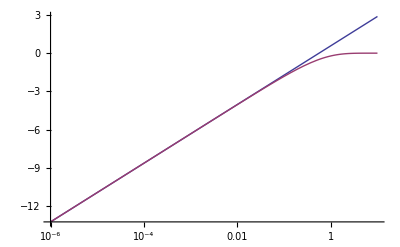

```mathematica
LogLinearPlot[{EA[x],ExpIntegralEi[-x]},{x,0.000001,10}]
```

```mathematica
rw=0.35;
μ=0.8;
ϕ=0.1;
k=10;
Export["expint.dat",Table[N[EA[x]],{x,{0.000001,0.000002,0.000003,0.000004,0.000005,0.000006,0.000007,0.000008,0.000009,0.00001,0.00002,0.00003,0.00004,0.00005,0.00006,0.00007,0.00008,0.00009,0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.0007,0.0008,0.0009,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,2,3,4,5,6,7,8,9,10
}}]]
```

expint.dat

```mathematica
N[ExpIntegralEi[-1]]
```

-0.219384